This script is to get the final version of the dabataBaseOPAL-UnCover-Colombia. We will use   dataBase20202021.csv and dataBaseAnalysis6.csv built in 4.dataAnalysisLoS.nb instead of casesOutcomefechas_G*.m, because these last are already processed in these databases.

In OPAL the Values are ALWAYS NUMERICAL. Missing is ALWAYS indicated with a “.”

## Data Bases

```mathematica
(*This is the most complete DataBase of COVID-19 patients from 17/03/2020 to 15/08/2021. With this DataBase we made the rest of the databases.*)
```

```mathematica
dataBase20202021=Import["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
dataBase20202021//Length
```

245372

```mathematica
dataBase20202021[[-1]]
```

{245375,4870036,76,VALLE,76001,CALI,85,1,M,,,9/8/2021 0:00:00,15/8/2021 0:00:00,Fallecido,16/8/2021 0:00:00,,Mon 16 Aug 2021,,Tue 17 Aug 2021,,,,,}

```mathematica
dataBase6=Import["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBaseAnalysis6.csv"];
```

```mathematica
dataBase6[[1]]//PositionIndex
```

<|ID→{1},ageYears→{2},ageG→{3},Gender→{4},IMP_M_2018→{5},IMP_D_2019→{6},IMP_D_2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26}|>

```mathematica
dataBase6//Length
```

245372

```mathematica
dataBase6[[-1]]
```

{245375,85,75_,M,11.9,10.8,11.1,Yes,2,1,1,0,1,0,NA,0,0,0,NA,0,0,0,NA,0,0,0}

Theses data bases are equivalent in the ID. But they have slightly different information about each case

```mathematica
(dataBase6[[2;;,4]]-dataBase20202021[[2;;,9]])//Tally
```

{{0,245365},{F-F ,5},{M-M ,1}}

## Ordering demographic data

```mathematica
DMRAGEYR=dataBase6[[2;;,2]];(*Age, Continuos Type, Years/Missing, 0-150/"."*)DMRAGEYR//Tally
```

{{34,2939},{85,1885},{74,3478},{68,4153},{48,3503},{61,4619},{54,4401},{59,4778},{37,3286},{21,1492},{31,2957},{72,3808},{22,1754},{49,3737},{29,2816},{69,4018},{57,4814},{51,3984},{65,4443},{53,4270},{88,1202},{28,2783},{25,2399},{26,2606},{41,3434},{58,4785},{70,4059},{62,4822},{45,3201},{64,4507},{47,3355},{52,4158},{76,3036},{80,2821},{84,1975},{56,4662},{87,1478},{30,2788},{40,3481},{83,2121},{63,4627},{20,1461},{38,3339},{42,3318},{23,1987},{43,3235},{66,4291},{3,486},{71,3731},{55,4528},{67,4390},{27,2567},{60,4968},{50,3861},{32,2905},{75,3361},{33,2895},{44,3284},{46,3160},{77,2937},{36,3076},{35,3131},{73,3505},{17,735},{12,449},{39,3303},{79,2815},{0.833333,121},{94,329},{1,1053},{82,2281},{95,251},{19,1298},{81,2446},{93,441},{90,921},{78,2852},{97,116},{15,580},{86,1635},{0.666667,144},{14,527},{6,344},{96,181},{91,710},{13,437},{2,649},{0.0833333,428},{24,2304},{89,977},{8,377},{18,860},{16,686},{92,604},{5,391},{9,404},{4,427},{10,397},{103,6},{0.166667,254},{0.0712329,19},{0.416667,172},{11,393},{0.5,179},{0.030137,17},{0.333333,179},{0.25,191},{7,419},{0.916667,117},{0.583333,129},{100,52},{0.0739726,14},{0.0767123,23},{0.00547945,32},{0.0328767,20},{0.0136986,16},{0.0410959,23},{0.75,155},{0.0794521,24},{0.00273973,29},{0.0630137,26},{0.0246575,8},{0.0109589,33},{0.0684932,20},{0.0465753,17},{0.0356164,29},{0.0164384,23},{0.00821918,30},{98,79},{0.0219178,17},{0.0520548,17},{99,49},{0.0493151,22},{0.0547945,31},{0.0383562,24},{0.0657534,21},{0.060274,12},{0.0273973,17},{0.0438356,26},{101,24},{106,4},{0.0191781,17},{107,2},{102,15},{0.0575342,12},{104,6},{105,2},{1.5,1}}

```mathematica
DMRGENDR=dataBase6[[2;;,4]]/.{"M"->0,"F"->1};(*Sex, Binary Type, Male/Female/Missing, 0/1/"."*)DMRGENDR//Tally
```

{{0,136365},{1,109006}}

```mathematica
dataBase20202021[[2;;,10]]//Tally (* 1:Indigena,2:ROM,3:Raizal,4:Palenquero,5 Negro,6:Otro*)
```

{{5,6271},{6,234877},{1,4152},{3,25},{2,12},{,34}}

```mathematica
{{5,6271},{6,234877},{1,4152},{3,25},{2,12},{"",34}}
```

```mathematica
DMRRETH1=dataBase20202021[[2;;,10]]/.{1->5,2->1,3->3,5->2,6->3,""->"."};(*Ethnicity, Categorical type, 1-Asian / 2-Black / 3-Hispanic / 4-White / 5-Multiracial / 6-Other / Missing, 1/2/3/4/5/.*)DMRRETH1//Tally
```

{{2,6271},{3,234902},{5,4152},{1,12},{.,34}}

```mathematica
(************************************************************)
```

```mathematica
data1={{"ID","DMRAGEYR","DMRGENDR","DMRRETH1",Sequence@@dataBase6[[1,9;;26]]},Sequence@@Map[Flatten,Transpose[{dataBase6[[2;;,1]],DMRAGEYR,DMRGENDR,DMRRETH1,dataBase6[[2;;,9;;26]]}]]};
```

```mathematica
data1[[1;;2]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT
1 | 34 | 0 | 2 | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0

```mathematica
data1[[-1]]
```

{245375,85,0,.,2,1,1,0,1,0,NA,0,0,0,NA,0,0,0,NA,0,0,0}

## Ordering dates data

### Deleting cases

```mathematica
(***********************with NAs in their pathway code*)
```

```mathematica
data1[[2;;,5]]//Tally
```

{{1,161773},{5,4683},{NA,5230},{4,13239},{7,3263},{2,32714},{6,3315},{3,18646},{11,113},{8,1717},{9,329},{12,105},{10,244}}

```mathematica
data1=Select[data1,#[[5]]!="NA"&];
```

```mathematica
data1[[2;;,5]]//Tally
```

{{1,161773},{5,4683},{4,13239},{7,3263},{2,32714},{6,3315},{3,18646},{11,113},{8,1717},{9,329},{12,105},{10,244}}

```mathematica
(************************with unexpected NAs in their pathways*)
```

```mathematica
dataBPH=Select[Select[data1,#[[5]]==1||#[[5]]==2&],#[[7]]!="NA"&];
dataBPICU=Select[Select[data1,#[[5]]==3||#[[5]]==4&],#[[11]]!="NA"&];
dataBPHICU=Select[Select[data1,#[[5]]==5||#[[5]]==7&],#[[7]]!="NA"&&#[[11]]!="NA"&];
dataBPICUH=Select[Select[data1,#[[5]]==6||#[[5]]==10&],#[[7]]!="NA"&&#[[11]]!="NA"&];
dataBPHICUH=Select[Select[data1,#[[5]]==8||#[[5]]==11&],#[[7]]!="NA"&&#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBPICUHICU=Select[Select[data1,#[[5]]==9||#[[5]]==12&],#[[7]]!="NA"&&#[[11]]!="NA"&&#[[19]]!="NA"&];
```

```mathematica
(*NOTA: Aqui vamos a tener más casos por rutas que en la base de datos 7 porque aqui no vamos a eliminar los casos con tiempos mayores a 100 días*)
```

```mathematica
dataBPH[[2;;,{7,11,15,19}]]/._?IntegerQ->t//Tally (*H,RD esperamos que todos los t esten en la primera posición*)
```

{{{t,NA,NA,NA},194486}}

```mathematica
dataBPICU[[2;;,{7,11,15,19}]]/._?IntegerQ->t//Tally (*ICU,RD esperamos que todos los t esten en la segunda posición*)
```

{{{NA,t,NA,NA},31884}}

```mathematica
{{{"NA",t,"NA","NA"},31064}}(*dataBase7*)
```

```mathematica
dataBPHICU[[2;;,{7,11,15,19}]]/._?IntegerQ->t//Tally (*H,ICU,RD esperamos que todos los t esten en la primera y segunda posición*)
```

{{{t,t,NA,NA},7945}}

```mathematica
{{{t,t,"NA","NA"},7758}}(*dataBase7*)
```

```mathematica
dataBPICUH[[2;;,{7,11,15,19}]]/._?IntegerQ->t//Tally (*ICU,H,RD esperamos que todos los t esten en la primera y segunda posición*)
```

{{{t,t,NA,NA},3558}}

```mathematica
{{{t,t,"NA","NA"},3439}}(*dataBase7*)
```

```mathematica
dataBPHICUH[[2;;,{7,11,15,19}]]/._?IntegerQ->t//Tally (*H,ICU,H,RD esperamos que todos los t esten en la primera y segunda y tercer posición*)
```

{{{t,t,t,NA},1829}}

```mathematica
{{{t,t,t,"NA"},1803}}(*dataBase7*)
```

```mathematica
dataBPICUHICU[[2;;,{7,11,15,19}]]/._?IntegerQ->t//Tally (*H,ICU,H,RD esperamos que todos los t esten en la primera y segunda y cuarta posición*)
```

```mathematica
{{{t,t,"NA",t},432}}(*dataBase7*)
```

```mathematica
(********************dataBase 7 no tiene casos con tiempos mayores a 100 días*)
```

```mathematica
dataBase7=Import["/home/lina/Documents/unCoVer/processingDataINS/outputOfScripts/dataBaseAnalysis7.csv"];
```

```mathematica
dataBase7//Length
```

245372

```mathematica
dataBPH7=Select[Select[dataBase7,#[[9]]==1||#[[9]]==2&],#[[11]]!="NA"&];
```

```mathematica
dataBPH7[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,RD esperamos que todos los t esten en la primera posición*)
```

{{{t,NA,NA,NA},184785}}

```mathematica
(***************************************************************)
```

```mathematica
(*NOTA: Este es el total de casos hospitalizados con las rutas correctas y sin eliminar los tiempos mayores a 100 días*)
```

```mathematica
data2={{"ID","DMRAGEYR","DMRGENDR","DMRRETH1",Sequence@@dataBase6[[1,9;;26]]},Sequence@@Join[dataBPH,dataBPICU,dataBPHICU,dataBPICUH,dataBPHICUH,dataBPICUHICU]};
```

```mathematica
data2//Length
```

240142

```mathematica
Length[dataBase6[[2;;,1]]]-Length[data2[[2;;,1]]]
```

5230

```mathematica
data2[[1;;3]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | BedPathway | timesBP | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | time2HOutcomeRDT | outcome2HR | outcome2HD | outcome2HT | time2ICUOutcomeRDT | outcome2ICUR | outcome2ICUD | outcome2ICUT
1 | 34 | 0 | 2 | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0
2 | 85 | 1 | 3 | 1 | 1 | 8 | 1 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0 | NA | 0 | 0 | 0

### Dates

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
dataBase20202021[[1]]
```

{ID,posINS,DeparmentC,DeparmentN,MunicipioC,MunicipioN,Age,AgeUnity,Gender,EthnicityC,EthnicityN,SymptomOnset,DateDiagnosis,outcomeINS,DateDeceased,DateRecovery,AdHospital,RecoveryH,DeceasedH,transferredICU,AdICU,RecoveryICU,DeceasedICU,transferredH}

```mathematica
(********************data3 son los seleccionados en data2 y extraidos de dataBase20202021)
```

```mathematica
Length[dataBase20202021]-1
```

245371

```mathematica
dataBase20202021[[-1]]
```

{245375,4870036,76,VALLE,76001,CALI,85,1,M,,,9/8/2021 0:00:00,15/8/2021 0:00:00,Fallecido,16/8/2021 0:00:00,,Mon 16 Aug 2021,,Tue 17 Aug 2021,,,,,}

```mathematica
p=Complement[dataBase20202021[[2;;,1]],data2[[2;;,1]]];
```

```mathematica
Length[dataBase6[[2;;,1]]]-Length[data2[[2;;,1]]]
```

5230

```mathematica
p//Length
```

5230

```mathematica
data3=DeleteCases[dataBase20202021[[2;;,{1,4,6,12,Sequence@@Range[17,24],2,3,5,11,13,14,15,16}]],{Alternatives[Sequence@@p],__}];
```

```mathematica
(data3[[All,1]]//Sort)-(data2[[2;;,1]]//Sort)//Tally
```

{{0,240141}}

```mathematica
data3[[1]]//Length
```

20

```mathematica
(************************data 4: fusion data3 y data2)
```

```mathematica
data4={{"ID","DMRAGEYR","DMRGENDR","DMRRETH1","BP","ID","Origen1D","Origen2M","FIS","AdHospital","RecoveryH","DeceasedH","transferredICU","AdICU","RecoveryICU","DeceasedICU","transferredH","posINS","DeparmentC","MunicipioC","EthnicityN","DateDiagnosis","outcomeINS","DateDeceased","DateRecovery"},Sequence@@Map[Flatten,Transpose[{data2[[2;;,1;;5]]//SortBy[#,First]&,data3//SortBy[#,First]&}]]};
```

```mathematica
data4[[1;;3]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | BP | ID | Origen1M | Origen2D | FIS | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH | posINS | DeparmentC | MunicipioC | EthnicityN | DateDiagnosis | outcomeINS | DateDeceased | DateRecovery
1 | 34 | 0 | 2 | 1 | 1 | VALLE | BUGA | 4/3/2020 0:00:00 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  |  | 3 | 76 | 76111 |  | 9/3/2020 0:00:00 | Recuperado |  | 19/3/2020 0:00:00
2 | 85 | 1 | 3 | 1 | 2 | CARTAGENA | CARTAGENA | 2/3/2020 0:00:00 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  |  | 8 | 13001 | 13001 |  | 11/3/2020 0:00:00 | Recuperado |  | 17/3/2020 0:00:00

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | BP | ID | FIS | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
1 | 34 | 0 | 2 | 1 | 1 | 4/3/2020 0:00:00 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  | 
2 | 85 | 1 | 3 | 1 | 2 | 2/3/2020 0:00:00 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  |

```mathematica
(data4[[2;;,1]]-data4[[2;;,6]])//Tally
```

{{0,240141}}

```mathematica
(*************************************************************************nombres del vector DATES**********)
```

DATSO : Date of symptom onset,                                                   yyyy - mm - dd / Missing,                                                                                 /.
DATAD : Date of Admission,                                                              yyyy - mm - dd / Missing,                                                                               /.
DATADI : Date of Admission to ICU,                                                yyyy - mm - dd / Missing,                                                                 /.
DATDSI: Date of discharge from ICU,                                           yyyy - mm - dd / Missing,                                                                 /.
DATDS: Date of discharge,                                                                 yyyy - mm - dd / Missing,                                                                 /.
DATLGT: Length of stay in hospital,                                                Days/Missing,                                                                 0-180/.
DATLGTI: Length of stay in ICU,                                                        Days/Missing,                                                                 0-180/.
DSXHO: Patient admitted to hospital,                                           No/Yes/Missing,                                                                 0/1/.
DSXIC: Patient admitted to ICU,                                                        No/Yes/Missing,                                                                  0/1/.
DSXOS: Outcome status,                                                                     Recovered/Deceased/Transferred/Missing,            0/1/2/.
DATOS: Date of outcome status ,                                                    yyyy - mm - dd / Missing,                                                        /.

DATAD is the date a patient starts occupying a regular non - ICU bed . If a patient enters hospital directly into ICU then DATADI will occur before DATAD
DATDS is the date of discharge by any cause, whether it be recovered, deceased or transferred to another hospital
DATLGT includes all days staying in hospital without considering ICU stay, DATLGTI includes all days staying within the ICU
In the case that all patients in your database are admitted to hospital, then yes, the answer to variable DSXHO will be "yes", and the same thing for DSXIC with respect to patients admitted to ICU

```mathematica
(******************rules: dependiendo de la BP los tiempos de la data4 se organizan de cierta manera para dar el vector de DATES*)
```

```mathematica
vectorDates={"DATAD","DATADI","DATDSI","DATDS","DATLGT","DATLGTI","DSXHO","DSXIC","DSXOS","DATOS"};
```

```mathematica
{{"AdHospital"-a, "RecoveryH"-b, "DeceasedH"-c, "transferredICU"-d, "AdICU"-e, "RecoveryICU"-f, "DeceasedICU"-g, "transferredH"}}-h
```

```mathematica
(*hay que revisar los que salen como DEceased porque las fechas cambian*)
```

```mathematica
rules={{1,a_,b_,c_,d_,e_,f_,g_,h_}->{a,".",".",b,b-a,".",1,0,0,b},{2,a_,b_,c_,d_,e_,f_,g_,h_}->{a,".",".",c,c-a,".",1,0,1,c},{3,a_,b_,c_,d_,e_,f_,g_,h_}->{".",e,f,".",".",f-e,0,1,0,f},{4,a_,b_,c_,d_,e_,f_,g_,h_}->{".",e,g,".",".",g-e,0,1,1,g},{5,a_,b_,c_,d_,e_,f_,g_,h_}->{a,e,f,f,e-a,f-e,1,1,0,f},{7,a_,b_,c_,d_,e_,f_,g_,h_}->{a,e,g,g,e-a,g-e,1,1,1,g},{6,a_,b_,c_,d_,e_,f_,g_,h_}->{h,e,h,b,b-h,h-e,1,1,0,b},{10,a_,b_,c_,d_,e_,f_,g_,h_}->{h,e,h,c,c-h,h-e,1,1,1,c}};(*No voy a incluir los casos con rutas 8-11-9-12 porque no es claro cuales tiempo de estas rutas deben ponerse aqui*)
```

```mathematica
d=data4[[2;;,{5,Sequence@@Range[10,17]}]]/.rules;
```

```mathematica
Count[data4[[;;,5]],8|11|9|12]
```

2264

```mathematica
data4[[1]]//PositionIndex
```

<|ID→{1,6},DMRAGEYR→{2},DMRGENDR→{3},DMRRETH1→{4},BP→{5},Origen1D→{7},Origen2M→{8},FIS→{9},AdHospital→{10},RecoveryH→{11},DeceasedH→{12},transferredICU→{13},AdICU→{14},RecoveryICU→{15},DeceasedICU→{16},transferredH→{17},posINS→{18},DeparmentC→{19},MunicipioC→{20},EthnicityN→{21},DateDiagnosis→{22},outcomeINS→{23},DateDeceased→{24},DateRecovery→{25}|>

```mathematica
data5={{"ID","DMRAGEYR","DMRGENDR","DMRRETH1","BP","Origen1D","Origen2M","DATSO","DATAD","DATADI","DATDSI","DATDS","DATLGT","DATLGTI","DSXHO","DSXIC","DSXOS","DATOS","AdHospital","RecoveryH","DeceasedH","transferredICU","AdICU","RecoveryICU","DeceasedICU","transferredH","posINS","DeparmentC","MunicipioC","EthnicityN","DateDiagnosis","outcomeINS","DateDeceased","DateRecovery"},Sequence@@Map[Flatten,Select[Transpose[{data4[[2;;,{1,2,3,4,5,7,8,9}]],d,data4[[2;;,10;;]]}],Length[#[[2]]]==10&],1]};
```

```mathematica
Length[data4[[2;;]]]-Length[data5]
```

2264

```mathematica
data5[[1;;2]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | BP | Origen1M | Origen2D | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
1 | 34 | 0 | 2 | 1 | VALLE | BUGA | 4/3/2020 0:00:00 | Sun 15 Mar 2020 | . | . | Mon 23 Mar 2020 | 8 days | . | 1 | 0 | 0 | Mon 23 Mar 2020

```mathematica
{{"ID", "DMRAGEYR", "D MRGENDR", "DMRRETH1", "DATSO", "DATAD", "DATADI", "DATDSI", "DATDS", "DATLGT", "DATLGTI", "DSXHO", "DSXIC", "DSXOS", "DATOS"}, {1, 34, 0, 2, "4/3/2020 0:00:00", DateObject[{2020,3,15},"Day","Gregorian",-5.], ".", ".", DateObject[{2020,3,23},"Day","Gregorian",-5.], Quantity[8, "Days"], ".", 1, 0, 0, DateObject[{2020,3,23},"Day","Gregorian",-5.]}}
```

```mathematica
data5[[2;;,8]]=If[#=="","",StringDrop[#,-8]]&/@data5[[2;;,8]];
```

```mathematica
data5[[1;;2]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | BP | Origen1M | Origen2D | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
1 | 34 | 0 | 2 | 1 | VALLE | BUGA | 4/3/2020 | Sun 15 Mar 2020 | . | . | Mon 23 Mar 2020 | 8 days | . | 1 | 0 | 0 | Mon 23 Mar 2020

```mathematica
Clear[newDate]
```

```mathematica
newDate[""]:="."
newDate["."]:="."
```

```mathematica
newDate["Missing"]:="Missing"
newDate[date_]:=Block[{$DateStringFormat={"Day","/","Month","/","Year"}},DateString[date[[1]]]]
```

```mathematica
day[""]:="."
day["."]:="."
day["Missing"]:="Missing"
day[quantity_/;Head[quantity]==Quantity]:=QuantityMagnitude[quantity]
```

```mathematica
data5[[2;;,9]]=newDate/@data5[[2;;,9]];
data5[[2;;,10]]=newDate/@data5[[2;;,10]];
data5[[2;;,11]]=newDate/@data5[[2;;,11]];
data5[[2;;,12]]=newDate/@data5[[2;;,12]];
data5[[2;;,13]]=day/@data5[[2;;,13]];
data5[[2;;,14]]=day/@data5[[2;;,14]];data5[[2;;,18]]=newDate/@data5[[2;;,18]];
```

```mathematica
data5[[2;;,1]]=Range[1,Length[data5]-1];
```

```mathematica
(****************************************revisando que la nueva base y la previa sean iguales ***)
```

```mathematica
previo=Import["/home/lina/Documents/unCoVer/processingDataINS/datosINS/dataOPAL/dataColombiaOPAL2.csv"];
```

```mathematica
data5[[1]]//PositionIndex
```

<|ID→{1},DMRAGEYR→{2},DMRGENDR→{3},DMRRETH1→{4},BP→{5},Origen1M→{6},Origen2D→{7},DATSO→{8},DATAD→{9},DATADI→{10},DATDSI→{11},DATDS→{12},DATLGT→{13},DATLGTI→{14},DSXHO→{15},DSXIC→{16},DSXOS→{17},DATOS→{18},AdHospital→{19},RecoveryH→{20},DeceasedH→{21},transferredICU→{22},AdICU→{23},RecoveryICU→{24},DeceasedICU→{25},transferredH→{26},posINS→{27},DeparmentC→{28},MunicipioC→{29},EthnicityN→{30},DateDiagnosis→{31},outcomeINS→{32},DateDeceased→{33},DateRecovery→{34}|>

```mathematica
previo[[1]]//PositionIndex
```

<|ID→{1},DMRAGEYR→{2},DMRGENDR→{3},DMRRETH1→{4},DATSO→{5},DATAD→{6},DATADI→{7},DATDSI→{8},DATDS→{9},DATLGT→{10},DATLGTI→{11},DSXHO→{12},DSXIC→{13},DSXOS→{14},DATOS→{15}|>

```mathematica
data5[[2;;35000,2]]==previo[[2;;,2]]
```

True

```mathematica
Export["/home/lina/Documents/unCoVer/processingDataINS/datosINS/dataOPAL/dataColombiaOPALv2.csv",data5]
```

/home/lina/Documents/unCoVer/processingDataINS/datosINS/dataOPAL/dataColombiaOPALv2.csv

```mathematica
(****************************************** de esta manera se crearon cada uno de las bases de datos de la primera versión del OPAL **)
```

```mathematica
Partition[Range[1,238000],35000][[All,{1,-1}]]
```

{{1,35000},{35001,70000},{70001,105000},{105001,140000},{140001,175000},{175001,210000}}

```mathematica
Apply[Export["/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL"<>ToString[#1]<>".csv",{data5[[1]],Sequence@@data5[[#1;;#2]]},"CSV"]&]/@{{2,35000},{35001,70000},{70001,105000},{105001,140000},{140001,175000},{175001,-1}}
```

{/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL2.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL35001.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL70001.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL105001.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL140001.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL175001.csv}

```mathematica
Apply[Histogram[#1, PlotLabel->#2<>" x:"<>ToString[Mean[DeleteCases[#1,"."]//N]]<>" IQR"<>ToString[InterquartileRange[DeleteCases[#1,"."]//N]]<>" n:"<>ToString[Length[DeleteCases[#1,"."]//N]],Frame->True,FrameLabel->{"times -days","#cases"},ImageSize->Medium]&]/@{{data5[[2;;,10]],"DARLGT"},{Select[data5,#[[14]]==0&][[2;;,10]],"DARLGT-R"},{Select[data5,#[[14]]==0&&#[[3]]==0&][[2;;,10]],"DARLGT-R-Male"},{Select[data5,#[[14]]==0&&#[[3]]==1&][[2;;,10]],"DARLGT-R-Female"},{Select[data5,#[[14]]==1&][[2;;,10]],"DARLGT-D"},{Select[data5,#[[14]]==1&&#[[3]]==0&][[2;;,10]],"DARLGT-D-Male"},{Select[data5,#[[14]]==1&&#[[3]]==1&][[2;;,10]],"DARLGT-D-Female"},{data5[[2;;,11]],"DARLGTI"},{Select[data5,#[[14]]==0&][[2;;,11]],"DARLGTI-R"},{Select[data5,#[[14]]==0&&#[[3]]==0&][[2;;,11]],"DARLGTI-R-Male"},{Select[data5,#[[14]]==0&&#[[3]]==1&][[2;;,11]],"DARLGTI-R-Female"},{Select[data5,#[[14]]==1&][[2;;,11]],"DARLGTI-D"},{Select[data5,#[[14]]==1&&#[[3]]==0&][[2;;,11]],"DARLGTI-D-Male"},{Select[data5,#[[14]]==1&&#[[3]]==1&][[2;;,11]],"DARLGTI-D-Female"}}
```

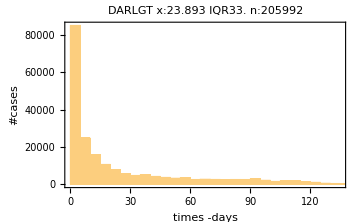
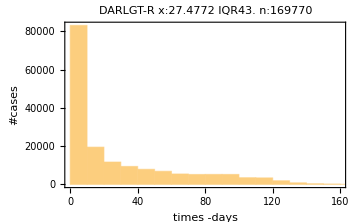
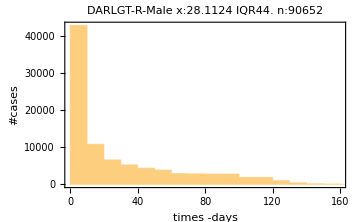
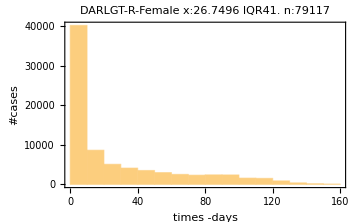
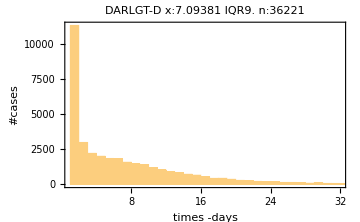
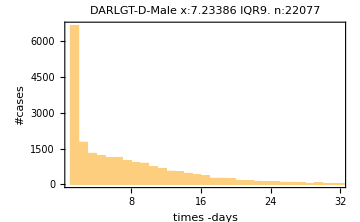
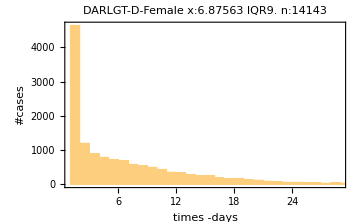
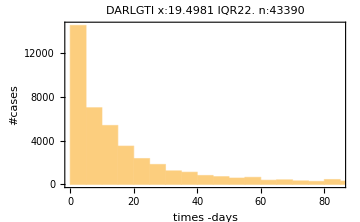

```mathematica
(************************************************************************ACUTUALIZACION DE LA DATA OPAL CON NUEVAS VARIABLES*)
```

```mathematica
depa=data5[[2;;,6]]//DeleteDuplicates
```

{VALLE,CARTAGENA,HUILA,BOGOTA,BARRANQUILLA,RISARALDA,ANTIOQUIA,STA MARTA D.E.,CUNDINAMARCA,QUINDIO,META,CALDAS,ATLANTICO,CAUCA,BOLIVAR,SANTANDER,CESAR,NORTE SANTANDER,BOYACA,CASANARE,TOLIMA,CORDOBA,NARIÑO,MAGDALENA,CHOCO,GUAJIRA,AMAZONAS,PUTUMAYO,ARAUCA,CAQUETA,SUCRE,GUAVIARE,VAUPES,VICHADA,SAN ANDRES,GUAINIA}

```mathematica
muni=data5[[2;;,7]]//DeleteDuplicates;
```

```mathematica
(******************************************)
```

```mathematica
additional=Import["/home/lina/Documents/unCoVer/processingDataINS/datosINS/dataOPAL/dataBaseAdditionaVars.csv"];
```

```mathematica
additional[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},Waves→{7},PeaksValleys1→{8},PeaksValleys2→{9},1BedPathway→{10},2BedPathway→{11},IPMDEP2019→{12},BLEDEP2019→{13},BASSDEP2019→{14},HCDEP2019→{15},IEEDEP2019→{16},SAFAMDEP2019→{17},SASDEP2019→{18},IPMDEP2020→{19},BLEDEP2020→{20},BASSDEP2020→{21},HCDEP2020→{22},IEEDEP2020→{23},SAFAMDEP2020→{24},SASDEP2020→{25},IPMM2020→{26},BLEM2020→{27},BASSM2020→{28},HCM2020→{29},IEEM2020→{30},SAFAMM2020→{31},SASM2020→{32}|>

```mathematica
varMun=Thread[additional[[2;;,4]]->additional[[2;;,{26,27,28,29,30,31,32}]]]//DeleteDuplicates;(* variables por municipio *)
```

```mathematica
Length@varMun
```

1009

```mathematica
varDep=Thread[additional[[2;;,5]]->additional[[2;;,{19,20,21,22,23,24,25}]]]//DeleteDuplicates;(* variables por departamento *)
```

```mathematica
Length@varDep
```

36

```mathematica
(************************************comparando las regiones entre ambas bases de datos*)
```

```mathematica
Complement[muni,varMun[[All,1]]]
```

{barrancabermeja ,DARIEN}

```mathematica
Complement[depa,varDep[[All,1]]]
```

{}

```mathematica
(****************************************************)
```

```mathematica
(*IPM : Indice de Pobreza Multidimensional
BLE : Bajo Logro Educativo
BASS : Barrera Acceso a los Servicios de Salud
HA : Hacinamiento Crítico
IEE : Inadecuada Eliminación de Excretas
SAAM : Sin Acceso a Agua Mejorada
SAS : Sin Aseguramiento en Salud *)
```

```mathematica
(**************************************)
```

```mathematica
additional2=Import["/home/lina/Documents/unCoVer/processingDataINS/prevalenciasEnfermedades.xlsx"];
```

```mathematica
additional2[[1,1]]//PositionIndex
```

<|COD_DEP→{1},DEP_NOM→{2},COD_MUN_DANE→{3},COD_MUN_INS→{4},MUN_NOM→{5},IPM_MUN→{6},PRE_HTA→{7},PRE_DM→{8},PRE_ERC→{9},PRE_CA→{10},POB_DANE→{11},DEB_POB→{12}|>

```mathematica
varMun2=Thread[additional2[[1,2;;,5]]->additional2[[1,2;;,{7,8,9,10}]]]//DeleteDuplicates;
```

```mathematica
varMun2[[1]]
```

EL ENCANTO→{0.,0.,0.,0.}

```mathematica
Length@varMun2
```

1122

```mathematica
Complement[muni,varMun2[[All,1]]]
```

{barrancabermeja ,DARIEN}

```mathematica
(***********************************************)
```

```mathematica
(*PRE_HTA:Prevalencia de hipertensión a nivel municipal
PRE_DM:Prevalencia de diabetes a nivel municipal
PRE_ERC:Prevalencia de enfermedad renal crónica a nivel municipal
PRE_CA:Tasa de cáncer a nivel municipal
Estas prevalencias son reportadas como una prevalencia de periodo en el año 2020 para cada una de las siguientes condiciones:prevalencia de hipertensión por cada 100 habitantes,
prevalencia de diabetes mellitus por cada 100 habitantes,prevalencia de enfermedad renal crónica por cada 100 habitantes y tasa de cáncer general invasivo por cada 100.000 habitantes*)
```

```mathematica
(***************************************************)
```

```mathematica
data5[[1]]//PositionIndex
```

<|ID→{1},DMRAGEYR→{2},DMRGENDR→{3},DMRRETH1→{4},BP→{5},Origen1D→{6},Origen2M→{7},DATSO→{8},DATAD→{9},DATADI→{10},DATDSI→{11},DATDS→{12},DATLGT→{13},DATLGTI→{14},DSXHO→{15},DSXIC→{16},DSXOS→{17},DATOS→{18},AdHospital→{19},RecoveryH→{20},DeceasedH→{21},transferredICU→{22},AdICU→{23},RecoveryICU→{24},DeceasedICU→{25},transferredH→{26},posINS→{27},DeparmentC→{28},MunicipioC→{29},EthnicityN→{30},DateDiagnosis→{31},outcomeINS→{32},DateDeceased→{33},DateRecovery→{34}|>

```mathematica
newOPAL={{"ID","DMRAGEYR","DMRGENDR","DMRRETH1","DATSO","DATAD","DATADI","DATDSI","DATDS","DATLGT","DATLGTI","DSXHO","DSXIC","DSXOS","DATOS","IPM20201","BLE20201","BASS20201","HC20201","IEE20201","SAFAM20201","SAS20201","IPM20202","BLEM20202","BASS20202","HC20202","IEE20202","SAFAM20202","SAS20202","PRE_HTA20202","PRE_DM20202","PRE_ERC20202","PRE_CA20202"},Sequence@@(data5[[2;;,{1,2,3,4,8,9,10,11,12,13,14,15,16,17,18,6,7,7}]]/."barrancabermeja "->"BARRANCABERMEJA")};
```

```mathematica
newOPAL[[;;4]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS | IPM20201 | BLE20201 | BASS20201 | HC20201 | IEE20201 | SAFAM20201 | SAS20201 | IPM20202 | BLEM20202 | BASS20202 | HC20202 | IEE20202 | SAFAM20202 | SAS20202 | PRE_HTA20202 | PRE_DM20202 | PRE_ERC20202 | PRE_CA20202
1 | 34 | 0 | 2 | 4/3/2020 0:00:00 | 15/03/2020 | . | . | 23/03/2020 | 8 | . | 1 | 0 | 0 | 23/03/2020 | VALLE | BUGA | BUGA |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2 | 85 | 1 | 3 | 2/3/2020 0:00:00 | 15/03/2020 | . | . | 23/03/2020 | 8 | . | 1 | 0 | 0 | 23/03/2020 | CARTAGENA | CARTAGENA | CARTAGENA |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3 | 74 | 1 | 3 | 6/3/2020 0:00:00 | 15/03/2020 | . | . | 25/03/2020 | 10 | . | 1 | 0 | 0 | 25/03/2020 | HUILA | NEIVA | NEIVA |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
newOPAL[[2;;,-3]]=newOPAL[[2;;,-3]]/.varDep;
newOPAL[[2;;,-2]]=newOPAL[[2;;,-2]]/.varMun/."DARIEN"->{"NA","NA","NA","NA","NA","NA","NA"};
newOPAL[[2;;,-1]]=newOPAL[[2;;,-1]]/.varMun2/."DARIEN"->{"NA","NA","NA","NA"};
```

```mathematica
newOPAL2=Flatten/@newOPAL;
```

```mathematica
newOPAL2[[;;3]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS | IPM20201 | BLE20201 | BASS20201 | HC20201 | IEE20201 | SAFAM20201 | SAS20201 | IPM20202 | BLEM20202 | BASS20202 | HC20202 | IEE20202 | SAFAM20202 | SAS20202 | PRE_HTA20202 | PRE_DM20202 | PRE_ERC20202 | PRE_CA20202
1 | 34 | 0 | 2 | 4/3/2020 0:00:00 | 15/03/2020 | . | . | 23/03/2020 | 8 | . | 1 | 0 | 0 | 23/03/2020 | 11.1 | 34.9 | 1.2 | 4.4 | 3. | 3.2 | 10.1 | 12.3 | 40.9 | 4.2 | 4.8 | 1.1 | 1.6 | 13.7 | 13.82 | 5.17 | 2.75 | 451.7
2 | 85 | 1 | 3 | 2/3/2020 0:00:00 | 15/03/2020 | . | . | 23/03/2020 | 8 | . | 1 | 0 | 0 | 23/03/2020 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 19.9 | 33.5 | 2.5 | 14.2 | 7.8 | 5.4 | 17.6 | 14.8 | 4.78 | 2.72 | 244.06

```mathematica
Export["/home/lina/Documents/unCoVer/processingDataINS/datosINS/dataOPAL/dataColombiaOPALv3.csv",newOPAL2];
```

```mathematica
Partition[Range[1,Length[newOPAL2]],48000][[All,{1,-1}]]
```

{{1,48000},{48001,96000},{96001,144000},{144001,192000}}

```mathematica
Apply[Export["/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL"<>ToString[#1]<>"v3.csv",{newOPAL2[[1]],Sequence@@newOPAL2[[#1;;#2]]},"CSV"]&]/@{{1,48000},{48001,96000},{96001,144000},{144001,-1}}
```

{/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL1v3.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL48001v3.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL96001v3.csv,/home/lina/Documents/UnCover/datos_INS/dataOPAL/dataColombiaOPAL144001v3.csv}

```mathematica
(***********PREVIOUS REVIEWING*)
```

```mathematica
Select[newOPAL[[2;;,-2]],StringQ[#]&]
```

{DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN}

```mathematica
{"DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN","barrancaber ¿meja ","DARIEN","DARIEN","DARIEN","DARIEN","DARIEN"}
```

```mathematica
MapAt[#/.varMun2&,MapAt[#/.varMun&,MapAt[#/.varDep&,data5[[2;;,{1,2,3,4,8,9,10,11,12,13,14,15,16,17,18,6,7,7}]],{All,-3}],{All,-2}],{All,-1}];
```

```mathematica
Select[%87[[2;;,-3]]//DeleteDuplicates,StringQ[#]&]
```

{}

```mathematica
data5[[2;;,7]]/.varMun
```

{{12.3,40.9,4.2,4.8,1.1,1.6,13.7},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{17.6,37.8,3.8,7.3,3.9,2.7,19.4},{17.6,37.8,3.8,7.3,3.9,2.7,19.4},{11.5,40.3,1.5,3.,0.5,1.,15.2},{9.,26.2,4.3,5.6,0.7,0.5,18.7},{9.,26.2,4.3,5.6,0.7,0.5,18.7},{9.,26.2,4.3,5.6,0.7,0.5,18.7},{9.,26.2,4.3,5.6,0.7,0.5,18.7},{17.4,29.,3.,13.5,2.1,1.,20.1},{9.,26.2,4.3,5.6,0.7,0.5,18.7},237855,{56.3,74.3,7.,10.4,31.5,35.6,21.7},{27.1,41.2,2.8,14.,18.,9.4,16.4},{15.9,38.8,3.7,6.3,5.2,6.7,17.5},{15.9,38.8,3.7,6.3,5.2,6.7,17.5},{39.9,76.5,3.9,3.6,25.7,37.1,12.2},{11.,30.7,3.2,5.1,2.4,3.3,19.8},{41.6,74.9,1.8,5.9,26.7,33.9,11.2},{19.2,49.9,0.8,8.6,1.5,3.6,16.1},{22.6,58.9,4.2,7.9,6.6,23.2,13.6},{21.4,39.6,7.5,13.5,4.6,3.6,20.3},{11.9,33.,4.1,4.8,1.5,0.9,17.7}}
 |  |  |  |

```mathematica
Select[data5[[2;;,7]]/.varMun,StringQ[#]&]
```

{DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,barrancabermeja ,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN}

```mathematica
Select[data5[[2;;,7]]/.varMun2,StringQ[#]&]
```

{DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN,barrancabermeja ,DARIEN,DARIEN,DARIEN,DARIEN,DARIEN}

```mathematica
%87[[2;;,-2]]//DeleteDuplicates
```